# Spatially Adaptive Finite Volume Method For Moment Models

This Mathematica file implements a spatially adaptive finite volume method for moment models. The spatial adaptivity allows the simulation to use a different number of moments (and so different models) in different parts of the domain. Currently, the setting is the following: the domain is divided in 2 subdomains. In the left subdomain, the number of moments (=: ML) is smaller than the number of moments (=: MR) in the right subdomain. 
In this code, the interface between the two models is at the shock.

## Construction of Spatially Adaptive Moment Model

Construction of the spatial discretization matrix of the models. The construction is split into transport part (Roe matrix and viscosity matrix) and source term part (relaxation).

### Source Term

Computation of source term.

#### Extended vector models

Construction of the source term matrix for the models using the extended vector.

```mathematica
ConstructSourceTerm[nxL_,nxR_,x1_,x2_,momentsLeft_,momentsRight_,Relaxation_,dt_]:=Block[{SourceMatrixLeft,SourceMatrixRight,SourceTermVectorLeft,SourceTermVectorRight,SourceTermVector},
(* For the RHS source term, we assume a BGK-type operator and we assume that the source term matrix is a diagonal matrix *)
SourceMatrixLeft =SparseArray[{{i_,i_}/;i>=4:>1},{momentsLeft,momentsLeft}];
SourceMatrixRight =SparseArray[{{i_,i_}/;i>=4:>1},{momentsRight,momentsRight}];

SourceMatrix =ConstantArray[0,{n+2,n+2}];

For[i=2,i<nxL,i++,
For[j=1,j<i,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}]
];
SourceMatrix[[i,i]]=SourceMatrixLeft;
For[j=i+1,j<nxL,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];
For[j=nxL,j<=n+2,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];
];

For[i=nxL,i<=n+1,i++,
For[j=1,j<nxL,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsLeft}]
];
For[j=nxL,j<i,j++,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
SourceMatrix[[i,i]]=SourceMatrixRight;
For[j=i+1,j++,j<=n+2,
SourceMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
];

SourceMatrix[[1,1]]=ConstantArray[0,{momentsLeft,momentsLeft}];
SourceMatrix[[n+2,n+2]]=ConstantArray[0,{momentsRight,momentsRight}];

SourceTermVectorLeft={0,0,0};
SourceTermVectorRight={0,0,0};

For[i=4,i<=momentsLeft,i++,
SourceTermVectorLeft=Append[SourceTermVectorLeft,1];
SourceTermVectorRight=Append[SourceTermVectorRight,1];
];
For[i=momentsLeft+1,i<=momentsRight,i++,
SourceTermVectorRight=Append[SourceTermVectorRight,1];
];
SourceTermVector={};
For[i=0,i<nxL-1,i++,
SourceTermVector=Join[SourceTermVector,SourceTermVectorLeft];
];
For[i=nxL-1,i<=n+1,i++,
SourceTermVector=Join[SourceTermVector,SourceTermVectorRight];
];
(* Obtain source term vector *)
SourceTermVector=-1/Relaxation*SourceTermVector;
SourceMatrix=1/Relaxation*SourceMatrix;

(* Obtain Exponential of source term vector *)
SourceTermVector=Exp[SourceTermVector*dt];

SourceTermMatrix=DiagonalMatrix[SourceTermVector];
];
```

#### Non-square matrix models

Construction of the source term for the model that used non-square matrices.

```mathematica
ConstructSourceTermNonSquare[nxL_,nxR_,x1_,x2_,momentsLeft_,momentsRight_,Relaxation_,dt_]:=Block[{SourceMatrixLeft,SourceMatrixRight,SourceTermVectorLeft,SourceTermVectorRight,SourceTermVector},
(* For the RHS source term, we assume a BGK-type operator and we assume that the source term matrix is a diagonal matrix *)
SourceMatrixLeft =SparseArray[{{i_,i_}/;i>=4:>1},{momentsLeft,momentsLeft}];
SourceMatrixRight =SparseArray[{{i_,i_}/;i>=4:>1},{momentsRight,momentsRight}];

SourceMatrixNonSquare =ConstantArray[0,{n+2,n+2}];

For[i=2,i<=nxL+1,i++,
For[j=1,j<i,j++,
SourceMatrixNonSquare[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}]
];
SourceMatrixNonSquare[[i,i]]=SourceMatrixLeft;
For[j=i+1,j<=nxL+1,j++,
SourceMatrixNonSquare[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];
For[j=nxL+2,j<=n+2,j++,
SourceMatrixNonSquare[[i,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];
];

For[i=nxL+2,i<=n+1,i++,
For[j=1,j<=nxL+1,j++,
SourceMatrixNonSquare[[i,j]]=ConstantArray[0,{momentsRight,momentsLeft}]
];
For[j=nxL+2,j<i,j++,
SourceMatrixNonSquare[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
SourceMatrixNonSquare[[i,i]]=SourceMatrixRight;
For[j=i+1,j++,j<=n+2,
SourceMatrixNonSquare[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
];

SourceMatrixNonSquare[[1,1]]=ConstantArray[0,{momentsLeft,momentsLeft}];
SourceMatrixNonSquare[[n+2,n+2]]=ConstantArray[0,{momentsRight,momentsRight}];

SourceTermVectorLeft={0,0,0};
SourceTermVectorRight={0,0,0};

For[i=4,i<=momentsLeft,i++,
SourceTermVectorLeft=Append[SourceTermVectorLeft,1];
SourceTermVectorRight=Append[SourceTermVectorRight,1];
];
For[i=momentsLeft+1,i<=momentsRight,i++,
SourceTermVectorRight=Append[SourceTermVectorRight,1];
];
SourceTermVector={};
For[i=0,i<nxL+1,i++,
SourceTermVector=Join[SourceTermVector,SourceTermVectorLeft];
];
For[i=nxL+1,i<=n+1,i++,
SourceTermVector=Join[SourceTermVector,SourceTermVectorRight];
];
(* Obtain source term vector *)
SourceTermVector=-1/Relaxation*SourceTermVector;
SourceMatrixNonSquare=1/Relaxation*SourceMatrixNonSquare;

(* Obtain Exponential of source term vector *)
SourceTermVector=Exp[SourceTermVector*dt];

SourceTermMatrixNonSquare=DiagonalMatrix[SourceTermVector];
];
```

### Construction of model at the interface between the two subdomains

There are different options for the model we use in the cell directly right of the interface between the left and the right subdomains, in which a different number of moments is used.

#### Using a modified system matrix at the boundary interface

```mathematica
(* Here we use a modified Roe linearization at the boundary interface *)
modifiedRoeMatrixAtInterface[]:=Block[{},

RoeModifiedBlockMatrix[[nxL+2,nxL+1]]=-ARight;
RoeModifiedBlockMatrix[[nxL+2,nxL+2]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeModifiedBlockMatrix[[nxL+2,nxL+3]]=ARight;
ViscosityModifiedBlockMatrix[[nxL+2,nxL+1]]=-QRight;
ViscosityModifiedBlockMatrix[[nxL+2,nxL+2]]=2*QRight;
ViscosityModifiedBlockMatrix[[nxL+2,nxL+3]]=-QRight;

RoeModifiedBlockMatrix[[nxL+1,nxL]]=-ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];
RoeModifiedBlockMatrix[[nxL+1,nxL+1]]=ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]-ARight;
RoeModifiedBlockMatrix[[nxL+1,nxL+2]]=ARight;
ViscosityModifiedBlockMatrix[[nxL+1,nxL]]=-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];
ViscosityModifiedBlockMatrix[[nxL+1,nxL+1]]=ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]+QRight;
ViscosityModifiedBlockMatrix[[nxL+1,nxL+2]]=-QRight;

RoeModifiedBlockMatrix[[nxL,nxL-1]]=-ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,0}}];
RoeModifiedBlockMatrix[[nxL,nxL]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeModifiedBlockMatrix[[nxL,nxL+1]]=ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];
ViscosityModifiedBlockMatrix[[nxL,nxL-1]]=-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,0}}];
ViscosityModifiedBlockMatrix[[nxL,nxL]]=2*ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];
ViscosityModifiedBlockMatrix[[nxL,nxL+1]]=-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];
];
```

#### Using non-square matrices

```mathematica
nonSquareMatricesAtInterface[]:=(

For[j=1,j<=nxL+1,j++,
RoeNonSquareBlockMatrices[[1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityNonSquareBlockMatrices[[1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=nxL+2,j<=n+2,j++,
RoeNonSquareBlockMatrices[[1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
ViscosityNonSquareBlockMatrices[[1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];

(* Rows corresponding to moment model of order ML *)
For[i=2,i<=nxL,i++,
RoeNonSquareBlockMatrices[[i,i-1]]=-ALeft;
RoeNonSquareBlockMatrices[[i,i]]=ConstantArray[0,{momentsLeft,momentsLeft}];
RoeNonSquareBlockMatrices[[i,i+1]]=ALeft;
ViscosityNonSquareBlockMatrices[[i,i-1]]=-QLeft;
ViscosityNonSquareBlockMatrices[[i,i]]=2*QLeft;
ViscosityNonSquareBlockMatrices[[i,i+1]]=-QLeft;

For[j=1,j<i-1,j++,
RoeNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=i+2,j<=nxL+1,j++,
RoeNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=nxL+2,j<=n+2,j++,
RoeNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
ViscosityNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];
];

RoeNonSquareBlockMatrices[[nxL+1,nxL]]=-ALeft;
RoeNonSquareBlockMatrices[[nxL+1,nxL+1]]=ConstantArray[0,{momentsLeft,momentsLeft}];
RoeNonSquareBlockMatrices[[nxL+1,nxL+2]]=ARight[[;;-(numberOfMomentsDifference+1),;;]];
ViscosityNonSquareBlockMatrices[[nxL+1,nxL]]=-QLeft;
ViscosityNonSquareBlockMatrices[[nxL+1,nxL+1]]=2*QLeft;
ViscosityNonSquareBlockMatrices[[nxL+1,nxL+2]]=-QRight[[;;-(numberOfMomentsDifference+1),;;]];
For[j=1,j<nxL,j++,
RoeNonSquareBlockMatrices[[nxL+1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityNonSquareBlockMatrices[[nxL+1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];
For[j=nxL+3,j<=n+2,j++,
RoeNonSquareBlockMatrices[[nxL+1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
ViscosityNonSquareBlockMatrices[[nxL+1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];

RoeNonSquareBlockMatrices[[nxL+2,nxL+1]]=-ARight[[;;,;;-(numberOfMomentsDifference+1)]];
RoeNonSquareBlockMatrices[[nxL+2,nxL+2]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeNonSquareBlockMatrices[[nxL+2,nxL+3]]=ARight;
ViscosityNonSquareBlockMatrices[[nxL+2,nxL+1]]=-QRight[[;;,;;-(numberOfMomentsDifference+1)]];
ViscosityNonSquareBlockMatrices[[nxL+2,nxL+2]]=2*QRight;
ViscosityNonSquareBlockMatrices[[nxL+2,nxL+3]]=-QRight;
For[j=1,j<=nxL,j++,
RoeNonSquareBlockMatrices[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityNonSquareBlockMatrices[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];
For[j=nxL+4,j<=n+2,j++,
RoeNonSquareBlockMatrices[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityNonSquareBlockMatrices[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

For[i=nxL+3,i<n+2,i++,
RoeNonSquareBlockMatrices[[i,i-1]]=-ARight;
RoeNonSquareBlockMatrices[[i,i]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeNonSquareBlockMatrices[[i,i+1]]=ARight;

ViscosityNonSquareBlockMatrices[[i,i-1]]=-QRight;
ViscosityNonSquareBlockMatrices[[i,i]]=2*QRight;
ViscosityNonSquareBlockMatrices[[i,i+1]]=-QRight;

For[j=1,j<=nxL+1,j++,
RoeNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL+2,j<i-1,j++,
RoeNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

For[j=i+2,j<=n+2,j++,
RoeNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
];

For[j=1,j<=nxL+1,j++,
RoeNonSquareBlockMatrices[[n+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityNonSquareBlockMatrices[[n+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL+2,j<=n+2,j++,
RoeNonSquareBlockMatrices[[n+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityNonSquareBlockMatrices[[n+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
)
```

### Construction matrix

Construction of the Roe matrix and the viscosity matrix.

```mathematica
ConstructMatrix[nxL_,nxR_,x1_,x2_,dx_,momentsLeft_,momentsRight_,Relaxation_,dt_]:=Block[{},

(* Define the model matrices *)
ALeft=SparseArray[{{i_,j_}/;i-j==1:>Sqrt[j],{i_,j_}/;j-i==1:>Sqrt[i]},{momentsLeft,momentsLeft}];
ARight=SparseArray[{{i_,j_}/;i-j==1:>Sqrt[j],{i_,j_}/;j-i==1:>Sqrt[i]},{momentsRight,momentsRight}];
CMax=Max[N[Abs[Eigenvalues[ARight]]]];

(* Define the numerical viscosity matrices *)
QLeft=IdentityMatrix[momentsLeft];
QRight=IdentityMatrix[momentsRight];

(* Initialize block matrices for the different models *)

RoeBlockMatrix=ConstantArray[0,{n+2,n+2}];
ViscosityBlockMatrix=ConstantArray[0,{n+2,n+2}];

RoeModifiedBlockMatrix = ConstantArray[0,{n+2,n+2}];
ViscosityModifiedBlockMatrix=ConstantArray[0,{n+2,n+2}];

RoeNonSquareBlockMatrices = ConstantArray[0,{n+2,n+2}];
ViscosityNonSquareBlockMatrices=ConstantArray[0,{n+2,n+2}];

(* CREATE THE SPATIAL DISCRETIZATION MATRIX BLOCK BY BLOCK *)

(* First row is a ghost row *)
For[j=1,j<=nxL-1,j++,
RoeBlockMatrix[[1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityBlockMatrix[[1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=nxL,j<=n+2,j++,
RoeBlockMatrix[[1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
ViscosityBlockMatrix[[1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];

(* Rows corresponding to moment model of order ML *)
For[i=2,i<nxL-1,i++,
RoeBlockMatrix[[i,i-1]]=-ALeft;
RoeBlockMatrix[[i,i]]=ConstantArray[0,{momentsLeft,momentsLeft}];
RoeBlockMatrix[[i,i+1]]=ALeft;
ViscosityBlockMatrix[[i,i-1]]=-QLeft;
ViscosityBlockMatrix[[i,i]]=2*QLeft;
ViscosityBlockMatrix[[i,i+1]]=-QLeft;

For[j=1,j<i-1,j++,
RoeBlockMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityBlockMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=i+2,j<=nxL-1,j++,
RoeBlockMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityBlockMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=nxL,j<=n+2,j++,
RoeBlockMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
ViscosityBlockMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];
];

(* Row nxL-1 (corresponds to vector nxL-2 because of the introduced ghost rows *) 
RoeBlockMatrix[[nxL-1,nxL-2]]=-ALeft;
RoeBlockMatrix[[nxL-1,nxL-1]]=ConstantArray[0,{momentsLeft,momentsLeft}];
RoeBlockMatrix[[nxL-1,nxL]]=ArrayPad[ALeft,{{0,0},{0,numberOfMomentsDifference}}];
ViscosityBlockMatrix[[nxL-1,nxL-2]]=-QLeft;
ViscosityBlockMatrix[[nxL-1,nxL-1]]=2*QLeft;
ViscosityBlockMatrix[[nxL-1,nxL]]=-ArrayPad[QLeft,{{0,0},{0,numberOfMomentsDifference}}];

For[j=1,j<nxL-2,j++,
RoeBlockMatrix[[nxL-1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityBlockMatrix[[nxL-1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=nxL+1,j<=n+2,j++,
RoeBlockMatrix[[nxL-1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
ViscosityBlockMatrix[[nxL-1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];

(* Row nxL (corresponds to vector nxL-1 because of the introduced ghost rows) *)

RoeBlockMatrix[[nxL,nxL-1]]=-ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,0}}];
RoeBlockMatrix[[nxL,nxL]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeBlockMatrix[[nxL,nxL+1]]=ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];
ViscosityBlockMatrix[[nxL,nxL-1]]=-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,0}}];
ViscosityBlockMatrix[[nxL,nxL]]=2*ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];
ViscosityBlockMatrix[[nxL,nxL+1]]=-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];

For[j=1,j<nxL-1,j++,
RoeBlockMatrix[[nxL,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityBlockMatrix[[nxL,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL+2,j<=n+2,j++,
RoeBlockMatrix[[nxL,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityBlockMatrix[[nxL,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

(* Row nxL+1 (correspond to vector nxL because of the introduced  ghost rows *)

RoeModifiedBlockMatrix[[nxL+1,nxL]]=-ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];
RoeModifiedBlockMatrix[[nxL+1,nxL+1]]=ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]-ARight;
RoeModifiedBlockMatrix[[nxL+1,nxL+2]]=ARight;
ViscosityModifiedBlockMatrix[[nxL+1,nxL]]=-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];
ViscosityModifiedBlockMatrix[[nxL+1,nxL+1]]=ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]+QRight;
ViscosityModifiedBlockMatrix[[nxL+1,nxL+2]]=-QRight;

For[j=1,j<=nxL-1,j++,
RoeBlockMatrix[[nxL+1,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityBlockMatrix[[nxL+1,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];
For[j=nxL+3,j<=n+2,j++,
RoeBlockMatrix[[nxL+1,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityBlockMatrix[[nxL+1,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

(* Row nxL+2 (corresponds to vector nxL+1 because of the introduced ghost rows *)
RoeBlockMatrix[[nxL+2,nxL+1]]=-ARight;
RoeBlockMatrix[[nxL+2,nxL+2]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeBlockMatrix[[nxL+2,nxL+3]]=ARight;
ViscosityBlockMatrix[[nxL+2,nxL+1]]=-QRight;
ViscosityBlockMatrix[[nxL+2,nxL+2]]=2*QRight;
ViscosityBlockMatrix[[nxL+2,nxL+3]]=-QRight;

For[j=1,j<nxL,j++,
RoeBlockMatrix[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityBlockMatrix[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];
RoeBlockMatrix[[nxL+2,nxL]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityBlockMatrix[[nxL+2,nxL]]=ConstantArray[0,{momentsRight,momentsRight}];
For[j=nxL+4,j<=n+2,j++,
RoeBlockMatrix[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityBlockMatrix[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

(* Rows corresponding to moment model of order MR (without the last one) *)
For[i=nxL+3,i<n+2,i++,
RoeBlockMatrix[[i,i-1]]=-ARight;
RoeBlockMatrix[[i,i]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeBlockMatrix[[i,i+1]]=ARight;

ViscosityBlockMatrix[[i,i-1]]=-QRight;
ViscosityBlockMatrix[[i,i]]=2*QRight;
ViscosityBlockMatrix[[i,i+1]]=-QRight;

For[j=1,j<nxL,j++,
RoeBlockMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityBlockMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL,j<i-1,j++,
RoeBlockMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityBlockMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

For[j=i+2,j<=n+2,j++,
RoeBlockMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityBlockMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
];

(* Last rows are ghost rows *)
For[j=1,j<nxL,j++,
RoeBlockMatrix[[n+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityBlockMatrix[[n+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL,j<=n+2,j++,
RoeBlockMatrix[[n+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityBlockMatrix[[n+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

(* Call methods for using a modified Roe matrix at the boundary interface and using the model with non-square matrices at the interface. *)
RoeModifiedBlockMatrix=RoeBlockMatrix;
ViscosityModifiedBlockMatrix=ViscosityBlockMatrix;
modifiedRoeMatrixAtInterface[];

RoeNonSquareBlockMatrices=RoeBlockMatrix;
ViscosityNonSquareBlockMatrices=ViscosityBlockMatrix;
nonSquareMatricesAtInterface[];

(* Obtain full matrices from their block form *)
RoeMatrix = ArrayFlatten[RoeBlockMatrix];
ViscosityMatrix = ArrayFlatten[ViscosityBlockMatrix];

RoeModifiedMatrix = ArrayFlatten[RoeModifiedBlockMatrix];
ViscosityModifiedMatrix = ArrayFlatten[ViscosityModifiedBlockMatrix];

RoeNonSquareMatrix = ArrayFlatten[RoeNonSquareBlockMatrices];
ViscosityNonSquareMatrix = ArrayFlatten[ViscosityNonSquareBlockMatrices];

(* Call the method that construct the source term *)
ConstructSourceTerm[nxL,nxR,x1,x2,momentsLeft,momentsRight,Relaxation,dt];
ConstructSourceTermNonSquare[nxL,nxR,x1,x2,momentsLeft,momentsRight,Relaxation,dt];

(* Obtain transport part of spatial discretization matrix from Roe block matrix and viscosity block matrix *)

BigAMatrixBlock=-1.0/(2*dx)*(RoeBlockMatrix+ViscosityBlockMatrix);
BigAMatrix = -1.0/(2*dx)*(RoeMatrix+ViscosityMatrix);

BigAMatrixBlockModified=-1.0/(2*dx)*(RoeModifiedBlockMatrix+ViscosityModifiedBlockMatrix);
BigAMatrixModified = -1.0/(2*dx)*(RoeModifiedMatrix+ViscosityModifiedMatrix);
BigAMatrixNonSquareMatrixBlock=-1.0/(2*dx)*(RoeNonSquareBlockMatrices+ViscosityNonSquareBlockMatrices);
BigAMatrixNonSquareMatrix = -1.0/(2*dx)*(RoeNonSquareMatrix+ViscosityNonSquareMatrix);

];
```

## Construction of Reference Solution

As reference solution, we consider the numerical solution we obtain if we used the bigger matrix in the whole domain.

### Source Term

Construction of the source term matrix for the reference system.

```mathematica
ConstructSourceTermReference[nxL_,nxR_,x1_,x2_,momentsLeft_,momentsRight_,Relaxation_,dt_]:=Block[{SourceMatrixRight,SourceTermVectorReference,SourceTermVectorRight},
(* For the RHS source term, we assume a BGK-type operator and we assume that the source term matrix is a diagonal matrix *)
SourceMatrixReference =ConstantArray[0,{n+2,n+2}];

SourceMatrixRight =SparseArray[{{i_,i_}/;i>=4:>1},{momentsRight,momentsRight}];

For[i=2,i<=n+1,i++,
For[j=1,j<i,j++,
SourceMatrixReference[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}]
];
SourceMatrixReference[[i,i]]=SourceMatrixRight;
For[j=i+1,j<=n+2,j++,
SourceMatrixReference[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
];

SourceMatrixReference[[1,1]]=ConstantArray[0,{momentsRight,momentsRight}];
SourceMatrixReference[[n+2,n+2]]=ConstantArray[0,{momentsRight,momentsRight}];

SourceTermVectorRight={0,0,0};

For[i=4,i<=momentsRight,i++,
SourceTermVectorRight=Append[SourceTermVectorRight,1];
];

SourceTermVectorReference={};
For[i=0,i<=n+1,i++,
SourceTermVectorReference=Join[SourceTermVectorReference,SourceTermVectorRight];
];

(* Obtain source term vector *)
SourceTermVectorReference=-1/Relaxation*SourceTermVectorReference;
SourceMatrixReference=1/Relaxation*SourceMatrixReference;

(* Obtain Exponential of source term vector *)
SourceTermVectorReference=Exp[SourceTermVectorReference*dt];

SourceTermMatrixReference=DiagonalMatrix[SourceTermVectorReference];
];
```

### Construction matrix

Construction of the Roe matrix and the viscosity matrix for the reference system.

```mathematica
ConstructMatrixReference[nxL_,nxR_,x1_,x2_,dx_,momentsLeft_,momentsRight_,Relaxation_,dt_]:=Block[{RoeReferenceBlock,ViscosityReferenceBlock},
RoeReferenceBlock = ConstantArray[0,{n+2,n+2}];
ViscosityReferenceBlock=ConstantArray[0,{n+2,n+2}];

(* CREATE THE SPATIAL DISCRETIZATION MATRIX BLOCK BY BLOCK *)

(* First row is a ghost row *)
For[j=1,j<=n+2,j++,
RoeReferenceBlock[[1,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityReferenceBlock[[1,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

(* All rows apart from the first and the last *)
For[i=2,i<=n+1,i++,
RoeReferenceBlock[[i,i-1]]=-ARight;
RoeReferenceBlock[[i,i]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeReferenceBlock[[i,i+1]]=ARight;
ViscosityReferenceBlock[[i,i-1]]=-QRight;
ViscosityReferenceBlock[[i,i]]=2*QRight;
ViscosityReferenceBlock[[i,i+1]]=-QRight;

For[j=1,j<i-1,j++,
RoeReferenceBlock[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityReferenceBlock[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

For[j=i+2,j<=n+2,j++,
RoeReferenceBlock[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityReferenceBlock[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
];

(* Last rows are ghost rows *)
For[j=1,j<=n+2,j++,
RoeReferenceBlock[[n+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityReferenceBlock[[n+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

(* Call the method that constructs the source term for the reference system *)
ConstructSourceTermReference[nxL,nxR,x1,x2,momentsLeft,momentsRight,Relaxation,dt];

(* Obtain full Roe matrix and full viscosity matrix from their block form *)
RoeReference = ArrayFlatten[RoeReferenceBlock];
ViscosityReference = ArrayFlatten[ViscosityReferenceBlock];

(* Obtain transport part of spatial discretization matrix for the reference system from Roe block matrix and viscosity block matrix *)
BigAMatrixReferenceBlock=-1.0/(2*dx)*(RoeReferenceBlock+ViscosityReferenceBlock);
BigAMatrixReference = -1.0/(2*dx)*(RoeReference+ViscosityReference);
];
```

## Simulation Setup

Initialize model: construct vector with initial values, set parameters and call the spatial discretization matrices constructor functions.

### Construct vector with initial values for the extended vector models

Construct vector with the chosen initial values, for the models using the extended vector.

```mathematica
InitializeVector[momentsLeft_,momentsRight_,paddingCondition_]:=
Block[{padding},
(* Construct initial vector for spatially adaptive simulation *)
Wraw={};
For[j=0,j<momentsLeft,j++,
Wraw=Append[Wraw,m0[j,xs[1]]];(* Zero order extrapolation for ghost cell *)
];
For[i=1,i<nxL-1,i++,
For[j=0,j<momentsLeft,j++,
Wraw=Append[Wraw,m0[j,xs[i]]];
];
];
For[j=0,j<momentsRight,j++,
Wraw=Append[Wraw,m0[j,xs[nxL-1]]]; (* the cell with index nxL-1 needs to implement a boundary condition. The value for the last moment is overridden in the simulation function. *)
];
For[j=0,j<momentsLeft,j++,
Wraw=Append[Wraw,m0[j,xs[nxL-1]]];
];
If[paddingCondition=="zero",
For[j=momentsLeft,j<momentsRight,j++,Wraw=Append[Wraw,0]]; (* set last moments in the extended vector to zero *)
];
If[paddingCondition=="neighbour",
For[j=momentsLeft,j<momentsRight,j++,Wraw=Append[Wraw,m0[j,xs[nxL+1]]]]; (* set the last moments in the extended vector as the last moments of the neighbouring vector *)
];
For[i=nxL+1,i<=n,i++,
For[j=0,j<momentsRight,j++,
Wraw=Append[Wraw,m0[j,xs[i]]];
];
];
For[j=0,j<momentsRight,j++,
Wraw=Append[Wraw,m0[j,xs[n]]]; (* Zero order extrapolation for ghost cell *)
];

(* Construct initial vector for reference solution *)
WrawReference={};
For[j=0,j<momentsRight,j++,
WrawReference=Append[WrawReference,m0[j,xs[1]]]; (* Zero order extrapolation for ghost cell *)
];
For[i=1,i<=n,i++,
For[j=0,j<momentsRight,j++,
WrawReference=Append[WrawReference,m0[j,xs[i]]];
];
];
For[j=0,j<momentsRight,j++,
WrawReference=Append[WrawReference,m0[j,xs[n]]]; (* Zero order extrapolation for ghost cell *)
];
];
```

### Construct vector with initial values for non-square matrix models

```mathematica
InitializeVectorNonSquare[momentsLeft_,momentsRight_]:=(

(* Construct initial vector for spatially adaptive simulation using non-square matrices *)
Wraw={};
For[j=0,j<momentsLeft,j++,
Wraw=Append[Wraw,m0[j,xs[1]]];(* Zero order extrapolation for ghost cell *)
];
For[i=1,i<=nxL,i++,
For[j=0,j<momentsLeft,j++,
Wraw=Append[Wraw,m0[j,xs[i]]];
];
];
For[i=nxL+1,i<=n,i++,
For[j=0,j<momentsRight,j++,
Wraw=Append[Wraw,m0[j,xs[i]]];
];
];
For[j=0,j<momentsRight,j++,
Wraw=Append[Wraw,m0[j,xs[n]]]; (* Zero order extrapolation for ghost cell *)
];

(* Construct initial vector for reference solution *)
WrawReference={};
For[j=0,j<momentsRight,j++,
WrawReference=Append[WrawReference,m0[j,xs[1]]]; (* Zero order extrapolation for ghost cell *)
];
For[i=1,i<=n,i++,
For[j=0,j<momentsRight,j++,
WrawReference=Append[WrawReference,m0[j,xs[i]]];
];
];
For[j=0,j<momentsRight,j++,
WrawReference=Append[WrawReference,m0[j,xs[n]]]; (* Zero order extrapolation for ghost cell *)
];
);
```

### Set up model

Set spatial discretization parameters and call the spatial discretization matrix construction functions.

```mathematica
InitializeModel[nxL_,nxR_,x1_,x2_,momentsLeft_,momentsRight_,Relaxation_]:=(

numberOfMomentsDifference=momentsRight-momentsLeft;
n=nxL+nxR;
(*positionInFrontOfShock=0;*) (* positionInFrontOfShock is not used anymore *)

dx=(x2-x1)/(nxL+nxR);


InitializeVector[momentsLeft,momentsRight,"zero"];

(* Initialize the collection of the moments *)
moments=Table[moment[i],{i,0,momentsRight-1}];
momentsReference=Table[momentReference[i],{i,0,momentsRight-1}];
momentsLoop=Table[moment[i],{i,0,momentsRight-1}];
For[i=0,i<momentsRight,i++,
moment[i]={};
momentReference[i]={};
];

(* Initialize the sum of the moments to check conservation *)
momentsSum=Table[momentSum[i],{i,0,momentsRight-1}];
momentsReferenceSum=Table[momentReferenceSum[i],{i,0,momentsRight-1}];
For[i=0,i<momentsRight,i++,
momentSum[i]=0;
momentReferenceSum[i]=0;
];

(* Choose time step *)
dt=Min[{1/Relaxation,0.3 dx/CMax}];

ConstructMatrix[nxL,nxR,x1,x2,dx,momentsLeft,momentsRight,Relaxation,dt];
ConstructMatrixReference[nxL,nxR,x1,x2,dx,momentsLeft,momentsRight,Relaxation,dt];
);
```

```mathematica
InitializeModelNonSquare[nxL_,nxR_,x1_,x2_,momentsLeft_,momentsRight_,Relaxation_]:=(

numberOfMomentsDifference=momentsRight-momentsLeft;
n=nxL+nxR;

dx=(x2-x1)/(nxL+nxR);
(* Create grid points *)
xs[i_]:=x1+dx*(i-0.5);

InitializeVectorNonSquare[momentsLeft,momentsRight];

(* Initialize the collection of the moments *)
moments=Table[moment[i],{i,0,momentsRight-1}];
momentsReference=Table[momentReference[i],{i,0,momentsRight-1}];
momentsLoop=Table[moment[i],{i,0,momentsRight-1}];
For[i=0,i<momentsRight,i++,
moment[i]={};
momentReference[i]={};
];

(* Initialize the sum of the moments to check conservation *)
momentsSum=Table[momentSum[i],{i,0,momentsRight-1}];
For[i=0,i<momentsRight,i++,
momentSum[i]={};
];

(* Choose time step *)
dt=0.01dx;

ConstructMatrix[nxL,nxR,x1,x2,dx,momentsLeft,momentsRight,Relaxation,dt];
ConstructMatrixReference[nxL,nxR,x1,x2,dx,momentsLeft,momentsRight,Relaxation,dt];
);
```

## Simulation Functions

Definition of the time stepping methods. Forward Euler with a splitting between transport and relaxation is implemented for the different models.

### Spatially Adaptive Moment Model With Weighted Sum (THIS METHOD IS NOT USED ANYMORE)

Using a weighted sum in the equation for the cell right of the interface between the two models.

```mathematica
(*ComputeS0[]:=Block[{norm,normRemainder},
(* Compute the values of the point s0 along the path *)
norm=0;
For[i=1,i<=momentsLeft,i++,
norm+=(W[[momentsLeft*nxL+i]]-W[[momentsLeft*nxL+momentsRight+i]])^2;
];
normRemainder=0;
For[i=momentsLeft+1,i<=momentsRight,i++,
normRemainder+=W[[momentsLeft*nxL+momentsRight+i]]^2;
];
If[Sqrt[norm]+Sqrt[normRemainder]==0,s0=0,s0=Sqrt[norm]/(Sqrt[norm]+Sqrt[normRemainder])];
Return[s0];
]*)
```

```mathematica
(*ConstructWeightedSum[]:=Block[{norm,normRemainder,WeightedSumRoe,WeightedSumViscosity,modelDiffA,modelDiffQ,AWeightedSumLastColumns,QWeightedSumLastColumns},
(* Compute the values of the point s0 along the path *)
s0=ComputeS0[];
(*
norm=0;
For[i=1,i<=momentsLeft,i++,
norm+=(W[[momentsLeft*nxL+i]]-W[[momentsLeft*nxL+momentsRight+i]])^2;
];
normRemainder=0;
For[i=momentsLeft+1,i<=momentsRight,i++,
normRemainder+=W[[momentsLeft*nxL+momentsRight+i]]^2;
];
If[Sqrt[norm]+Sqrt[normRemainder]==0,s0=0,s0=Sqrt[norm]/(Sqrt[norm]+Sqrt[normRemainder])];
*)
(* THE SYSTEM MATRIX HERE IS A WEIGHTED SUM OF THE BIGGER MATRIX AND THE SMALLER MATRIX *)
s0=0.5;
WeightedSumRoe=s0*ATilde+(1-s0)*ARight;
WeightedSumViscosity=s0*QTilde+(1-s0)*QRight;

modelDiffA=ATilde-ARight;
modelDiffQ=QTilde-QRight;

AWeightedSumLastColumns=WeightedSumRoe;
QWeightedSumLastColumns=WeightedSumViscosity;
AWeightedSumLastColumns[[All,1;;momentsLeft]]=0;
QWeightedSumLastColumns[[All,1;;momentsLeft]]=0;

WeightedSumRoe[[All,-numberOfMomentsDifference;;-1]]=0;
WeightedSumViscosity[[All,-numberOfMomentsDifference;;-1]]=0;

BigAMatrixWeightedSumFlatten[[momentsLeft*nxL+momentsRight+1;;momentsLeft*nxL+momentsRight*2,momentsLeft*nxL+1;;momentsLeft*nxL+momentsRight]]= -1/(2*dx)*(-WeightedSumRoe-WeightedSumViscosity);
BigAMatrixWeightedSumFlatten[[momentsLeft*nxL+momentsRight+1;;momentsLeft*nxL+momentsRight*2,momentsLeft*nxL+momentsRight+1;;momentsLeft*nxL+momentsRight*2]]= -1/(2*dx)*(s0*modelDiffA-AWeightedSumLastColumns+2*QRight+s0*modelDiffQ-QWeightedSumLastColumns);
BigAMatrixWeightedSumFlatten[[momentsLeft*nxL+momentsRight+1;;momentsLeft*nxL+momentsRight*2,momentsLeft*nxL+2*momentsRight+1;;momentsLeft*nxL+momentsRight*3]]= -1/(2*dx)*(ARight-QRight);
]*)
```

```mathematica
(*FiniteVolumeSchemeWeightedSum[tend_]:=(
(* Reset variables *)
W=Wraw;
time= 0.0;
step=0;

{timeSpatiallyAdaptiveWeightedSum,outputSpatiallyAdaptive}=
AbsoluteTiming[
While[time<tend,
ConstructWeightedSum[];

(* SPLITTING OF EQUATION IN TRANSPORT STEP AND RELAXATION STEP *)
(* Transport step *)
W=W+dt*BigAMatrixWeightedSumFlatten.W;

(* Relaxation step *)
W=SourceTermMatrix.W;

(* Update boundary conditions *)
For[i=0,i<momentsLeft,i++,
W[[i+1]]=W[[i+1+momentsLeft]];
];
For[i=0,i<momentsRight,i++,
W[[momentsLeft*nxL+momentsRight*(nxR+1)+i+1]]=W[[momentsLeft*nxL+momentsRight*nxR+i+1]];
];

(* Update collection of each moment *)
For[i=0,i<momentsRight,i++,
momentLoop[i]={};
];

For[i=0,i<nxL,i++,
For[j=0,j<momentsLeft,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*i+j+1]]]
]
];
For[i=0,i<=nxR+1,i++,
For[j=0,j<momentsRight,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*nxL+momentsRight*i+j+1]]]
]
];

For[i=0,i<momentsRight,i++,
moment[i]=momentLoop[i];
];

(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
density=moment[0];
velocity=moment[1]/density;
temperature=(√2*moment[2]-density*velocity*velocity+density)/density;


time = time+dt;
step++;
]
];
);*)
```

### Spatially Adaptive Moment Model Using Padded Vector and Modified Roe Linearization At Boundary Interface

Using the bigger model in the equation for the cell right of the interface between the two models.

```mathematica
FiniteVolumeSchemeModifiedRoe[tend_]:=(
(* Reset variables *)
W=Wraw;
time= 0.0;
step=0;

{timeSpatiallyAdaptiveModifiedRoe,outputModifiedRoe}=
AbsoluteTiming[
While[time<tend,
(* SPLITTING OF EQUATION IN TRANSPORT STEP AND RELAXATION STEP *)
(* Transport step *)
W=W+dt*BigAMatrixModified.W;

(* Relaxation step *)
W=SourceTermMatrix.W;

(* Update boundary conditions *)
For[i=0,i<momentsLeft,i++,
W[[i+1]]=W[[i+1+momentsLeft]]; (* Update left boundary condition *)
];
For[i=momentsLeft,i<momentsRight,i++,
W[[momentsLeft*(nxL-1)+i+1]]=W[[momentsLeft*(nxL-1)+momentsRight+i+1]] (* Boundary interface boundary condition for the padded moments *)
];
For[i=0,i<momentsRight,i++,
W[[momentsLeft*(nxL-1)+momentsRight*(nxR+2)+i+1]]=W[[momentsLeft*(nxL-1)+momentsRight*(nxR+1)+i+1]]; (* Update right boundary condition *)
];

(* Update collection of each moment *)
For[i=0,i<momentsRight,i++,
momentLoop[i]={};
];

For[i=0,i<nxL,i++,
For[j=0,j<momentsLeft,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*i+j+1]]]
]
];
For[i=0,i<=nxR+1,i++,
For[j=0,j<momentsRight,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*nxL+momentsRight*i+j+1]]]
]
];

For[i=0,i<momentsRight,i++,
moment[i]=momentLoop[i];
];

For[i=0,i<momentsRight,i++,
momentSum[i]=Total[moment[i]];
];

(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
density=moment[0];
velocity=moment[1]/density;
temperature=(√2*moment[2]-density*velocity*velocity+density)/density;


time = time+dt;
step++;
]
];
);
```

### Spatially Adaptive Moment Model Using Padded Vector

Using the model for the non-zero-padded extended vector model in the equation for the cell right of the interface between the two models.

```mathematica
FiniteVolumeSchemePadded[tend_]:=(
(* Reset variables *)
W=Wraw;
time= 0.0;
step=0;

{timeSpatiallyAdaptivePadded,outputSpatiallyAdaptivePadded}=
AbsoluteTiming[
While[time<tend,
(* Update boundary conditions *)
For[i=0,i<momentsLeft,i++,
W[[i+1]]=W[[i+1+momentsLeft]]; (* Update left boundary condition *)
];
For[i=momentsLeft,i<momentsRight,i++,
W[[momentsLeft*(nxL-1)+i+1]]=W[[momentsLeft*(nxL-1)+momentsRight+i+1]] (* Boundary interface boundary condition for the padded moments *)
];
For[i=0,i<momentsRight,i++,
W[[momentsLeft*(nxL-1)+momentsRight*(nxR+2)+i+1]]=W[[momentsLeft*(nxL-1)+momentsRight*(nxR+1)+i+1]]; (* Update right boundary condition *)
];

(* SPLITTING OF EQUATION IN TRANSPORT STEP AND RELAXATION STEP *)
(* Transport step *)
W=W+dt*BigAMatrix.W;

(* Relaxation step *)
W=SourceTermMatrix.W;

(* Update collection of each moment *)
For[i=0,i<momentsRight,i++,
momentLoop[i]={};
];

For[i=0,i<nxL-1,i++,
For[j=0,j<momentsLeft,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*i+j+1]]]
]
];
For[i=0,i<=nxR+2,i++,
For[j=0,j<momentsRight,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*(nxL-1)+momentsRight*i+j+1]]]
]
];

For[i=0,i<momentsRight,i++,
moment[i]=momentLoop[i];
];

For[i=0,i<momentsRight,i++,
momentSum[i]=Total[moment[i]];
];

(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)

density=moment[0];
velocity=moment[1]/density;
temperature=(√2*moment[2]-density*velocity*velocity+density)/density;


time = time+dt;
step++;
]
];
);
```

### Spatially Adaptive Moment Model with using non-square matrices

```mathematica
FiniteVolumeSchemeNonSquareMatrices[tend_]:=(
(* Reset variables *)
W=Wraw;
time= 0.0;
step=0;

{timeSpatiallyAdaptiveNonSquareMatrices,outputSpatiallyAdaptive}=
AbsoluteTiming[
While[time<tend,
(* SPLITTING OF EQUATION IN TRANSPORT STEP AND RELAXATION STEP *)
(* Transport step *)
W=W+dt*BigAMatrixNonSquareMatrix.W;

(* Relaxation step *)
W=SourceTermMatrixNonSquare.W;

(* Update boundary conditions *)
For[i=0,i<momentsLeft,i++,
W[[i+1]]=W[[i+1+momentsLeft]];
];
For[i=0,i<momentsRight,i++,
W[[momentsLeft*(nxL+1)+momentsRight*nxR+i+1]]=W[[momentsLeft*(nxL+1)+momentsRight*(nxR-1)+i+1]];
];

(* Update collection of each moment *)
For[i=0,i<momentsRight,i++,
momentLoop[i]={};
];

For[i=0,i<=nxL,i++,
For[j=0,j<momentsLeft,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*i+j+1]]]
]
];
For[i=1,i<=nxR+1,i++,
For[j=0,j<momentsRight,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*(nxL+1)+momentsRight*(i-1)+j+1]]]
]
];

For[i=0,i<momentsRight,i++,
moment[i]=momentLoop[i];
];

(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
density=moment[0];
velocity=moment[1]/density;
temperature=(√2*moment[2]-density*velocity*velocity+density)/density;


time = time+dt;
step++;
]
];
);
```

### Reference Solution

Time stepping method for the reference solution.

```mathematica
FiniteVolumeSchemeReference[tend_]:=Block[{},
WReference=WrawReference;
time= 0.0;
step=0;

{timeReference,outputReference}=
AbsoluteTiming[
While[time<tend,
(* SPLITTING OF EQUATION IN TRANSPORT STEP AND RELAXATION STEP *)
(* Transport step *)
WReference=WReference+dt*BigAMatrixReference.WReference;

(* Relaxation step *)
WReference=SourceTermMatrixReference.WReference;

(* Update boundary conditions *)
For[i=0,i<momentsRight,i++,
WReference[[i+1]]=WReference[[i+1+momentsRight]];
WReference[[momentsRight*nxL+momentsRight*(nxR+1)+i+1]]=WReference[[momentsRight*nxL+momentsRight*nxR+i+1]];
];

(* Update collection of each moment *)
For[i=0,i<momentsRight,i++,
momentLoop[i]={};
];

For[i=0,i<=n+1,i++,
For[j=0,j<momentsRight,j++,
momentLoop[j]=Append[momentLoop[j],WReference[[momentsRight*i+j+1]]];
];
];

For[i=0,i<momentsRight,i++,
momentReference[i]= momentLoop[i];
];

For[i=0,i<momentsRight,i++,
momentReferenceSum[i]=Total[momentReference[i]];
];

(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
densityReference=momentReference[0];
velocityReference=momentReference[1]/densityReference;
temperatureReference=(√2*momentReference[2]-densityReference*velocityReference*velocityReference+densityReference)/densityReference;

time = time+dt;
step++;
]
];
];
```

### Comparison between reference solution and spatially adaptive moment models

Simultaneous simulation of spatially adaptive moment model and reference solution

```mathematica
FiniteVolumeSchemeComparison[tend_]:=Block[{norm,normRemainder,WeightedSumRoe,WeightedSumViscosity,modelDiffA,modelDiffQ},
(* Reset variables *)
W=Wraw;
WReference=WrawReference;
time= 0.0;
step=0;

{timeSpatiallyAdaptive,outputSpatiallyAdaptive}=
AbsoluteTiming[
While[time<tend,


(* Transport step *)
W=W+dt*BigAMatrix.W;
WReference=WReference+dt*BigAMatrixReference.WReference;

(* Relaxation step *)
W=SourceTermMatrix.W;
WReference=SourceTermMatrixReference.WReference;

(* Update boundary conditions *)
For[i=0,i<momentsLeft,i++,
W[[i+1]]=W[[i+1+momentsLeft]];
];
For[i=0,i<momentsRight,i++,
W[[momentsLeft*nxL+momentsRight*(nxR+1)+i+1]]=W[[momentsLeft*nxL+momentsRight*nxR+i+1]];
WReference[[i+1]]=WReference[[i+1+momentsRight]];
WReference[[momentsRight*nxL+momentsRight*(nxR+1)+i+1]]=WReference[[momentsRight*nxL+momentsRight*nxR+i+1]];
];

(* Update collection of each moment *)
For[i=0,i<momentsRight,i++,
momentLoop[i]={};
momentReferenceLoop[i]={};
];

For[i=0,i<nxL,i++,
For[j=0,j<momentsLeft,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*i+j+1]]]
]
];
For[i=0,i<=nxR+1,i++,
For[j=0,j<momentsRight,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*nxL+momentsRight*i+j+1]]]
]
];

For[i=0,i<=n+1,i++,
For[j=0,j<momentsRight,j++,
momentReferenceLoop[j]=Append[momentReferenceLoop[j],WReference[[momentsRight*i+j+1]]];
];
];

For[i=0,i<momentsRight,i++,
moment[i]=momentLoop[i];
momentReference[i]= momentReferenceLoop[i];
];

(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
density=moment[0];
velocity=moment[1]/density;
temperature=(√2*moment[2]-density*velocity*velocity+density)/density;
densityReference=momentReference[0];
velocityReference=momentReference[1]/densityReference;
temperatureReference=(√2*momentReference[2]-densityReference*velocityReference*velocityReference+densityReference)/densityReference;


time = time+dt;
step++;
]
];
];
```

## Numerical Data Post Processing

The moments might not have a direct physical interpretation. Some physical quantities are retrieved here.

```mathematica
(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
density=moment[0];
velocity=moment[1]/density;
temperature=(√2*moment[2]-density*velocity*velocity+density)/density;
densityReference=momentReference[0];
velocityReference=momentReference[1]/densityReference;
temperatureReference=(√2*momentReference[2]-densityReference*velocityReference*velocityReference+densityReference)/densityReference;
```

## Numerical Results

Set parameters:
- Number of grid points in each part of the subdomain
- Boundaries of the physical domain
- Number of moments in the left and the right subdomain
- Set initial values
- Set relaxation time

The model is then initialized by calling the InitializeModel function that takes the chosen parameters as arguments. To run the simulation, one more parameter is needed:
- Choose end time

Finally, one of the finite volume methods is called and one of the moments is dynamically plotted.

### Template

One can start from this template to initialize the model.

```mathematica
(* Choose number of cells in left and right subdomain *)
nxL = 100;
nxR = 100;

(* Choose boundaries of the spatial domain *)
x1=-10;
x2=10;

(* Choose number of moments in left and right subdomain *)
momentsLeft=4;
momentsRight=5;

(* Choose initial values *)
initialValuesLeft={1,1,1};
initialValuesRight={1,1,1};
epsilon=1.0;
momentsBig=0.0;

(* Choose relaxation parameter *)
Relaxation=1.0;

InitializeModel[nxL,nxR,x1,x2,momentsLeft,momentsRight,initialValuesLeft,initialValuesRight,epsilon,momentsBig,Relaxation]

(* Choose end time *)
tend=1.0;
```

```mathematica
(*Dynamic[ListPlot[moment[3],PlotRange->{-1,1}]]*)
Dynamic[ListPlot[moment[4]]]
FiniteVolumeSchemeWeightedSum[tend]
```

### Test Cases

#### Constant values

The simplest case is the case in which the moments have the same value in the whole domain.

```mathematica
(* Choose number of cells in left and right subdomain *)
nxL =50;
nxR = 50;

(* Choose boundaries of the spatial domain *)
x1=-10;
x2=10;

(* Choose number of moments in left and right subdomain *)
momentsLeft=4;
momentsRight=5;

(* Choose initial values *)
m0[0,x_]=1;
m0[1,x_]=0;
m0[2,x_]=1;
m0[3,x_]=1;
m0[4,x_]=0.1;

(* Choose relaxation parameter *)
Relaxation=1.0;

InitializeModel[nxL,nxR,x1,x2,momentsLeft,momentsRight,Relaxation]

(* Choose end time *)
tend=1.0;
```

```mathematica
(*Dynamic[ListPlot[moment[2],PlotRange->{2.999,3.001}]]*)
Dynamic[ListPlot[momentReference[3],AxesLabel->{x,Subscript[m, 0]},PlotRange->{0.,1.2}]]
Dynamic[momentReferenceSum[3]]

FiniteVolumeSchemeReference[tend]
```

#### Different density

```mathematica
(* Choose number of cells in left and right subdomain *)
nxL = 100;
nxR = 300;

(* Choose boundaries of the spatial domain *)
x1=-1;
x2=3;

(*create grid cells *)
xs[i_]:=x1+dx*(i-0.5);

(* Choose number of moments in left and right subdomain *)
momentsLeft=4;
momentsRight=5;

(* Choose initial values *)
m0[0,x_]:=If[x<1.5,2,1];
m0[1,x_]:=0;
m0[2,x_]:=0;
m0[3,x_]:=0.5;
m0[4,x_]:=0.1;

(* Choose relaxation parameter *)
Relaxation=1.0;

InitializeModel[nxL,nxR,x1,x2,momentsLeft,momentsRight,Relaxation]

(* Choose end time *)
tend=0.25;
```

```mathematica
Dynamic[ListPlot[moment[0],PlotRange->{0.9,2.1}]]
Dynamic[momentSum[0]]
(*time: 19.3030047*)
FiniteVolumeSchemePadded[tend]
```

```mathematica
Dynamic[ListPlot[momentReference[0],PlotRange->{0.9,2.1}]]
Dynamic[momentReferenceSum[0]]
(*time: 26.7947376*)
FiniteVolumeSchemeReference[tend]
```

```mathematica
simulationValues=Table[{xs[i],moment[0][[i]],moment[1][[i]],moment[2][[i]]},{i,1,n}]//MatrixForm;
Export["shockTube_Relaxation1.0_Mesh100+300_spatiallyAdaptiveZero.txt",simulationValues,"CSV"]
```

shockTube_Relaxation1.0_Mesh100+300_spatiallyAdaptiveZero.txt

```mathematica
"shockTube_Relaxation1.0_Mesh100+300_spatiallyAdaptiveZero.txt"
```

shockTube_Relaxation1.0_Mesh250+250_spatiallyAdaptiveZero.txt

```mathematica
simulationReference=Table[{xs[i],momentReference[0][[i]],momentReference[1][[i]],momentReference[2][[i]]},{i,1,n}]//MatrixForm;
Export["shockTube_Relaxation1.0_Mesh100+300_Reference.txt",simulationValues,"CSV"]
```

shockTube_Relaxation1.0_Mesh100+300_Reference.txt

```mathematica
timeReference
```

26.7947

```mathematica
timeSpatiallyAdaptivePadded
```

19.303

## Stability analysis

### Eigenvalues of the full spatial discretization matrix

```mathematica
(* Obtain the full spatial discretization matrix *)

StabilityMatrix = BigAMatrix-ArrayFlatten[SourceMatrix];
StabilityMatrixModified= BigAMatrixModified-ArrayFlatten[SourceMatrix];
StabilityMatrixReference= BigAMatrixReference-ArrayFlatten[SourceMatrixReference];
```

```mathematica
(* This computes the eigenvalues of the spatial discretization matrix *)

eigenvaluesStabilityMatrix=Eigenvalues[StabilityMatrix];
realPartEigenvalues =Re[eigenvaluesStabilityMatrix];
imaginaryPartEigenvalues  =Im[eigenvaluesStabilityMatrix ];
realPartEigenvaluesSorted=Sort[realPartEigenvalues];

eigenvaluesStabilityMatrixModified=Eigenvalues[StabilityMatrixModified];
realPartEigenvaluesModified =Re[eigenvaluesStabilityMatrixModified];
imaginaryPartEigenvaluesModified =Im[eigenvaluesStabilityMatrixModified];
realPartEigenvaluesModifiedSorted=Sort[realPartEigenvaluesModified];

eigenvaluesStabilityMatrixReference =Eigenvalues[StabilityMatrixReference];
realPartEigenvaluesReference =Re[eigenvaluesStabilityMatrixReference];
imaginaryPartEigenvaluesReference =Im[eigenvaluesStabilityMatrixReference];
realPartEigenvaluesReferenceSorted=Sort[realPartEigenvaluesReference];
```

```mathematica
(* This computes the eigenvalue with the biggest real part *)
Eigenvalues[StabilityMatrix,1,Method->{"Arnoldi","Criteria"->"RealPart","MaxIterations"->10000}]
```

{2.13855×10^-15}

#### Plotting

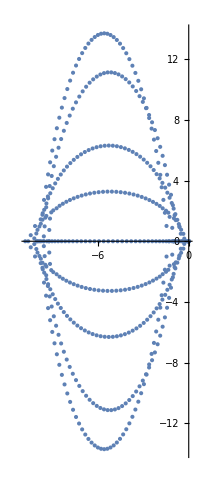

```mathematica
ComplexListPlot[eigenvaluesStabilityMatrix]
```

```mathematica
ComplexListPlot[eigenvaluesStabilityMatrixReference]
```

Eigenvalues::eival: Unable to find all roots of the characteristic polynomial.

ComplexListPlot::ldata: Eigenvalues[{{0. - 2.5 RoeReference, 0. - 2.5 RoeReference, 0. - 2.5 RoeReference, 0. - 2.5 RoeReference, 0. - 2.5 RoeReference, 0. - 2.5 RoeReference, 0. - 2.5 RoeReference, 0. - 2.5 <<11>>e, <<498>>, 0. - 2.5 RoeReference, 0. - 2.5 RoeReference, 0. - 2.5 RoeReference, 0. - 2.5 RoeReference}, <<509>>}] is not a valid dataset or list of datasets.

ComplexListPlot[Eigenvalues[{{0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,461,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference},508,{1}}]]
 |  |  |  |

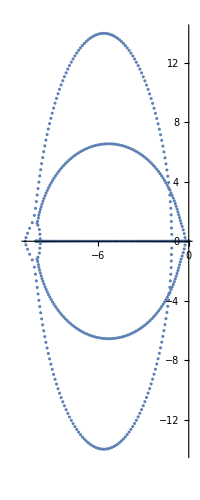

```mathematica
ComplexListPlot[eigenvaluesStabilityMatrixReference]
```